```mathematica
Manipulate[
Module[{unit},
unit[P1_,P2_,T1_,T2_,W_,η_]:=Graphics[{
{EdgeForm@Thick,FaceForm@Opacity[0.5,RGBColor[0.,0.96,0.72]],If[rh==1,Polygon[{{0,0},{1,0.25},{1,0.75},{0,1}}],Polygon[{{0,0.25},{1,0},{1,1},{0,0.75}}]]},
{Thick,Arrowheads@Large,Arrow[{{-0.5,0.5},{0,0.5}}],Arrow[{{1,0.5},{1.5,0.5}}]},
Text[Style[Column[{
Row[{Subscript[Style["P",Italic],1]," = ",P1," bar"}],Spacer[10],
Row[{Subscript[Style["T",Italic],1]," = ",T1," K"}]
},Alignment->"="],17],{-0.5,0.5}],
Text[Style[Column[{
Row[{Subscript[Style["P",Italic],2]," = ",P2," bar"}],Spacer[10],
Row[{Subscript[Style["T",Italic],2]," = ",T2," K"}]
},Alignment->"="],17],{1.5,0.5}],
Text[Style[Row[{Style["W",Italic]," = ",W," J"}],17],{0.5,1.05}],
Text[Column[{Style[If[rh==1,"compressor","turbine"],18],Style[Row[{Style["η",Italic]," = ",η," %"}],17]},Center],{0.5,0.5}]
},ImageSize->350];
Column[{unit[P1,P2,T1,T2,W,η],Spacer[20],unit[P1,P2,T1,T2,W,η]}]
],
Control[{{rh,1,""},{1->" compressors ",2->" turbines "},Setter}]
]
```

```mathematica
Module[{},
δx=0.5;
δy=
unit[c_]:=Polygon[{{c[[1]]-δx,
```

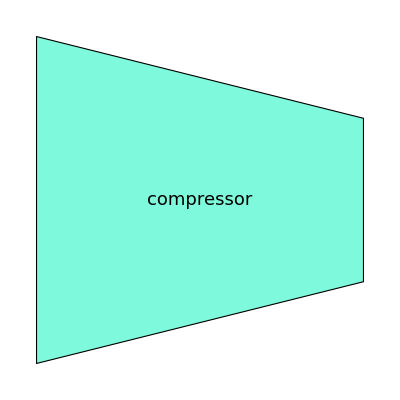

```mathematica
Graphics[{EdgeForm@Thick,FaceForm@Opacity[0.5,RGBColor[0.,0.96,0.72]],Polygon[{{0,0},{1,0.25},{1,0.75},{0,1}}],Text[Style["compressor",18],{0.5,0.5}]}]
```